# 本征值

```mathematica
Clear["Global`*"]
```

## 定义窗口Map

```mathematica
SubMovingMap[f_,list_,n_]:=Module[{len},len=Length[list];Map[f[Sequence@@Table[list[[#+i]],{i,0,n-1}]]&,Table[i,{i,1,len-n+1}]]]
```

```mathematica
MovingMapAt[f_,list_,n_,lev_]:=Piecewise[{{Map[SubMovingMap[f,#,n]&,Level[list,lev-1]],lev>=2},{SubMovingMap[f,list,n],lev==1}}]
```

```mathematica
MovingMapAt[(#1-#2)&,{{1,2,4},{4,5,6},{7,8,9}},2,2]
```

{{-1,-2},{-1,-1},{-1,-1}}

## 公式

```mathematica
hh=({{1.5+1/6+1/12*Cos[2*Pi/3]+1, 0.75(((Cos[-Pi/12]-I*Sin[-Pi/12])kx)-(Sin[-Pi/12]+I*Cos[-Pi/12])ky), 1/12, 1/12, 1/12*Exp[-I*2*Pi/3], 1/12, 1/12*Exp[I*2*Pi/3], 1/12}, {0.75(((Cos[-Pi/12]+I*Sin[-Pi/12])kx)-(Sin[-Pi/12]-I*Cos[-Pi/12])ky), 1.5+1/6+Cos[2*Pi/3]/6, 1/12, 1/12, 1/12*Exp[I*2*Pi/3], 1/12*Exp[-I*2*Pi/3], 1/12*Exp[-I*2*Pi/3], 1/12*Exp[I*2*Pi/3]}, {1/12, 1/12, 1.5+1/6, 0.75(((Cos[Pi/12]-I*Sin[Pi/12])kx)-(Sin[Pi/12]+I*Cos[Pi/12])ky), 0, 0, 0, 0}, {1/12, 1/12, 0.75(((Cos[Pi/12]+I*Sin[Pi/12])kx)-(Sin[Pi/12]-I*Cos[Pi/12])ky), 1.5+1/6, 0, 0, 0, 0}, {1/12*Exp[I*2*Pi/3], 1/12*Exp[-I*2*Pi/3], 0, 0, 1.5+Cos[2*Pi/3]/6, 0.75(((Cos[Pi/12]-I*Sin[Pi/12])kx)-(Sin[Pi/12]+I*Cos[Pi/12])ky), 0, 0}, {1/12, 1/12*Exp[I*2*Pi/3], 0, 0, 0.75(((Cos[Pi/12]+I*Sin[Pi/12])kx)-(Sin[Pi/12]-I*Cos[Pi/12])ky), 1.5+1/12+1/12*Cos[2*Pi/3], 0, 0}, {1/12*Exp[-I*2*Pi/3], 1/12*Exp[I*2*Pi/3], 0, 0, 0, 0, 1.5+Cos[2*Pi/3]/6, 0.75(((Cos[Pi/12]-I*Sin[Pi/12])kx)-(Sin[Pi/12]+I*Cos[Pi/12])ky)}, {1/12, 1/12*Exp[-I*2*Pi/3], 0, 0, 0, 0, 0.75(((Cos[Pi/12]+I*Sin[Pi/12])kx)-(Sin[Pi/12]-I*Cos[Pi/12])ky), 1.5+1/12+1/12*Cos[2*Pi/3]}})
```

{{2.625,0.75 (((ⅈ (-1+√3))/(2 √2)+(1+√3)/(2 √2)) kx-(-(-1+√3)/(2 √2)+(ⅈ (1+√3))/(2 √2)) ky),1/12,1/12,1/12 ⅇ^(-(2 ⅈ π)/3),1/12,1/12 ⅇ^((2 ⅈ π)/3),1/12},{0.75 ((-(ⅈ (-1+√3))/(2 √2)+(1+√3)/(2 √2)) kx-(-(-1+√3)/(2 √2)-(ⅈ (1+√3))/(2 √2)) ky),1.58333,1/12,1/12,1/12 ⅇ^((2 ⅈ π)/3),1/12 ⅇ^(-(2 ⅈ π)/3),1/12 ⅇ^(-(2 ⅈ π)/3),1/12 ⅇ^((2 ⅈ π)/3)},{1/12,1/12,1.66667,0.75 ((-(ⅈ (-1+√3))/(2 √2)+(1+√3)/(2 √2)) kx-((-1+√3)/(2 √2)+(ⅈ (1+√3))/(2 √2)) ky),0,0,0,0},{1/12,1/12,0.75 (((ⅈ (-1+√3))/(2 √2)+(1+√3)/(2 √2)) kx-((-1+√3)/(2 √2)-(ⅈ (1+√3))/(2 √2)) ky),1.66667,0,0,0,0},{1/12 ⅇ^((2 ⅈ π)/3),1/12 ⅇ^(-(2 ⅈ π)/3),0,0,1.41667,0.75 ((-(ⅈ (-1+√3))/(2 √2)+(1+√3)/(2 √2)) kx-((-1+√3)/(2 √2)+(ⅈ (1+√3))/(2 √2)) ky),0,0},{1/12,1/12 ⅇ^((2 ⅈ π)/3),0,0,0.75 (((ⅈ (-1+√3))/(2 √2)+(1+√3)/(2 √2)) kx-((-1+√3)/(2 √2)-(ⅈ (1+√3))/(2 √2)) ky),1.54167,0,0},{1/12 ⅇ^(-(2 ⅈ π)/3),1/12 ⅇ^((2 ⅈ π)/3),0,0,0,0,1.41667,0.75 ((-(ⅈ (-1+√3))/(2 √2)+(1+√3)/(2 √2)) kx-((-1+√3)/(2 √2)+(ⅈ (1+√3))/(2 √2)) ky)},{1/12,1/12 ⅇ^(-(2 ⅈ π)/3),0,0,0,0,0.75 (((ⅈ (-1+√3))/(2 √2)+(1+√3)/(2 √2)) kx-((-1+√3)/(2 √2)-(ⅈ (1+√3))/(2 √2)) ky),1.54167}}

## 定义将分段直线化为参数方程的函数

```mathematica
Km={4Pi/(3*Sqrt[3]*a),0,0}+4Pi/(3*Sqrt[3]*a)*Sin[the/2]*{0,-1,0};
Kmp={4Pi/(3*Sqrt[3]*a),0,0}+4Pi/(3*Sqrt[3]*a)*Sin[the/2]*{0,1,0};
Γm={4Pi/(3*Sqrt[3]*a),0,0}+4Pi/(3*Sqrt[3]*a)*Sqrt[3]*{1,0,0};Mm={4Pi/(3*Sqrt[3]*a),0,0}+4Pi/(3*Sqrt[3]*a)*{Sqrt[3]/2,-3/2,0};
```

```mathematica
ToParametric[x_,y_,d_][t_]:=Module[{len,arg},len=RegionMeasure[Line[{x,y}]];
arg={VectorAngle[y-x,{1,0,0}],VectorAngle[y-x,{0,1,0}],VectorAngle[y-x,{0,0,1}]};
Return[ConditionalExpression[t Cos[arg],0+d<t<len+d]]]
```

```mathematica
ToParametricMult[x__][t_]:=Module[{new,ang,len,lenn},
new=Differences[{x}];
ang=Map[Function[a,Map[Function[b,VectorAngle[a,b]],{{1,0,0},{0,1,0},{0,0,1}}]],new];
len=Map[RegionMeasure,MovingMapAt[Line[{#1,#2}]&,{x},2,1]];
lenn=Join[{0},Accumulate[len]];
Return[Piecewise[Table[{{x}[[i]]+(t-lenn[[i]]) Cos[ang[[i]]],lenn[[i]]<t<lenn[[i+1]]},{i,1,Length[ang]}]]]
]
```

```mathematica
fun[t_]:=ToParametricMult[Km,Kmp,Γm,Mm,Km][t]/.{the->Pi/6,a->1}
```

```mathematica
fun[j]//N
```

Piecewise[{{{2.4184,-0.625928+j,0.}, 0.<j<1.25186}, {{2.4184+0.989019 (-1.25186+j),0.625928-0.147788 (-1.25186+j),0.}, 1.25186<j<5.48715}, {{6.60719+0.5 (5.48715-1. j),-0.866025 (-5.48715+j),0.}, 5.48715<j<9.67594}, {{4.51279-0.572219 (-9.67594+j),-3.6276+0.820101 (-9.67594+j),0.}, 9.67594<j<13.3361}, {0., True}}]

```mathematica
RegionMeasure[Line[{Km,Kmp,Γm,Mm,Km}]]/.{a->1,the->Pi/6}//N
```

13.3361

```mathematica
ParametricPlot3D[{fun[t][[1]],fun[t][[2]],fun[t][[3]]},{t,0,13.3}]
```

-Graphics3D-

特征值表格

```mathematica
table=Table[{ba,Eigenvalues[hh/.{kx->fun[ba][[1]],ky->fun[ba][[2]]}]},{ba,0.1,13.336069304709,0.1}];
```

```mathematica
eva[n_]:=Riffle[table[[All,1]],table[[All,2,n]]]//Partition[#,2]&
```

作图

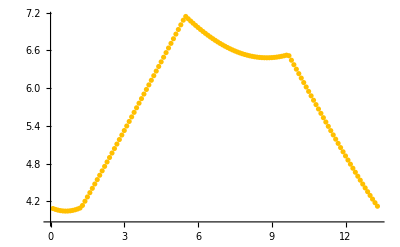
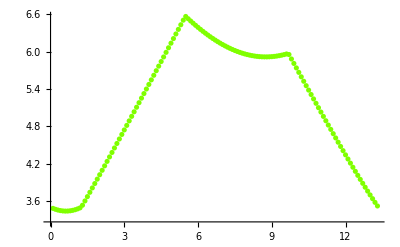
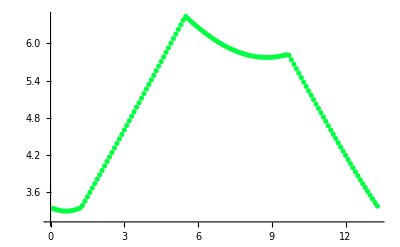
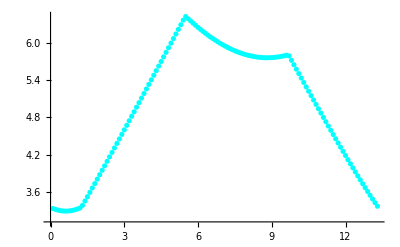
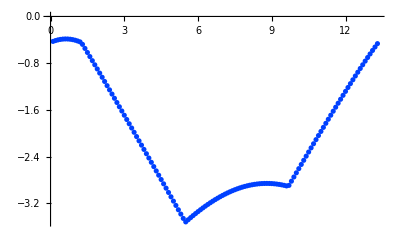
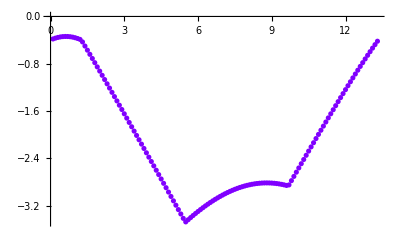
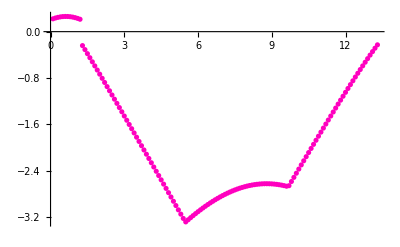
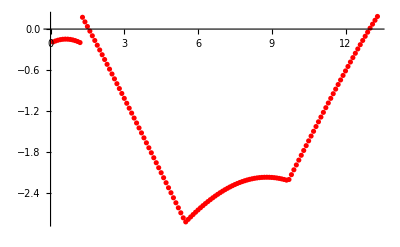

```mathematica
Table[ListPlot[Riffle[table[[All,1]],table[[All,2,i]]]//Partition[#,2]&,PlotRange->All,PlotStyle->Hue[i/Dimensions[hh][[1]]]],{i,1,Dimensions[hh][[1]]}]
```

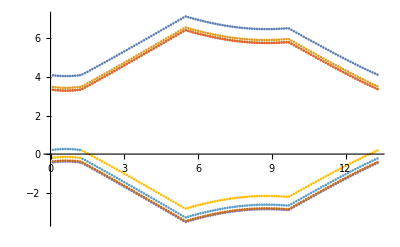

```mathematica
ListPlot[Table[eva[i],{i,1,8}]]
```